```mathematica
tasks = {
	Sin[2*x^3]^2/x^3
	, (x^2 - 4)*Sin[(Pi*(x^2))/6] / (x^2 - 1)
	, Sqrt[Abs[3*x^3 + 2*x^2 - 10*x]] / (4*x)
	, 1/2 * Log[Sqrt[x^2 + 1] / Sqrt[x^2 - 1]] - 15*x^2
	, (x^3 - x^2 - x + 1)^(1/3) / Tan[x]
	, 2*Log[(x - 1) / x] + 1
	, Log[x - 1] / (x - 1)^2
}
```

{(Sin[2 x^3]^2)/x^3,((-4+x^2) Sin[(π x^2)/6])/(-1+x^2),(√Abs[-10 x+2 x^2+3 x^3])/(4 x),-15 x^2+1/2 Log[(√(1+x^2))/(√(-1+x^2))],(1-x-x^2+x^3)^(1/3) Cot[x],1+2 Log[(-1+x)/x],Log[-1+x]/(-1+x)^2}

```mathematica
getVariantForNumber[number_, variationsQuo_]:=(
	Module[{t},
  t = Mod[number , variationsQuo];
  If[t ≠ 0
    , t
    , variationsQuo
   ]
	]
)
```

```mathematica
(* Проверяем, что все графики строятся нормально *)
Table[Plot[tasks[[i]], {x, -10, 10}], {i, 1, Length[tasks]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
yourNumber = 14  (*сюда вбить ваш номер по списку в рейтинге *)

numberOfYourTask = getVariantForNumber[yourNumber, Length[tasks]]

Print["Номер вашего задания: ", numberOfYourTask]

f[y_] := tasks[[numberOfYourTask]]/.x->y;

f[x]//TraditionalForm
```

14

7

Номер вашего задания: 7

(log(x-1))/(x-1)^2

```mathematica
(*1.Построить график*)
Plot[
	f[x]
	, {x, -10, 10}
]
```

-Graphics-

```mathematica
(*2.Является ли функция четной, нечетной, прочей*)
res1 = f[x] == f[-x] //TautologyQ
res2 = f[x] + f[-x] == 0 //TautologyQ
If[res1, "Функция четная", Null]
If[res2, "Функция нечетная", Null]
If[Not[res1||res2], "Функция прочая", Null]
```

False

False

Функция прочая

```mathematica
(*3. Область определения функции*)
FunctionDomain[f[x], x]
```

x>1

```mathematica
(*4.Периодичность функции*)
FunctionPeriod[f[x], x]
```

0

```mathematica
(*Так как FunctionPeriod выдала 0, то периода у функции нет*)

(*5.Точки пересечения графика с осями координат*)
sols = Solve[f[x]==0, x]
points = {x, 0}/.sols  (*вместо правил замены получаем список точек путем операции подстановки*)
g1 = Plot[f[x], {x, -10, 10}, PlotStyle->Blue];
g2 = ListPlot[points, PlotStyle->{Red, PointSize[Large]}];
Show[{g1, g2}]
```

{{x→2}}

{{2,0}}

-Graphics-

{{x→2}}

{{2,0}}

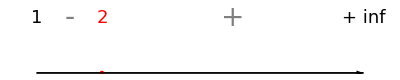

```mathematica
(*6. Промежутки знакопостоянства*)
sols = Solve[f[x]==0, x]
points = {x, 0}/.sols  (*вместо правил замены получаем список точек путем операции подстановки*)
g1 = Graphics[Line[{{0,0}, {10,0}}]];
g2 = ListPlot[points, PlotStyle->{Red, PointSize[Large]}];
g3 = Graphics[Text[Style["+", 28,Gray], {6, 0.5}]];
g4 = Graphics[Text[Style["-", 28, Gray], {1, 0.5}]];
g5 = Graphics[Text[Style["2", 18,Red], {2, 0.5}]];
g6 = Graphics[Text[Style["1", 18], {0, 0.5}]];
g7 = Graphics[Text[Style["+ inf", 18], {10, 0.5}]];
g8 = Graphics[Arrow[{{0,0}, {10,0}}]];
Show[{g1, g2, g3,g4,g5, g6, g7,g8}]
```

```mathematica
(*7. Экстремумы функции и значения в этих точках*)

sols = Solve[f'[x] == 0, x];
point =x /. sols
f[point]
```

{1+√ⅇ}

{1/(2 ⅇ)}

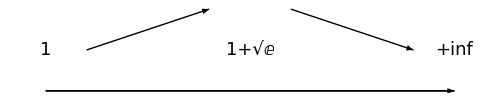

```mathematica
g1 = Graphics[Line[{{0,0}, {10,0}}]];
g2 = Graphics[Text[Style["1", 18], {0, 0.5}]];
g3 = Graphics[Text[Style[point[[1]], 18], {5, 0.5}]];
g4 = Graphics[Text[Style["+inf", 18], {10, 0.5}]];
g5 = Graphics[Arrow[{{1,0.5}, {4,1}}]];
g6 = Graphics[Arrow[{{6,1}, {9,0.5}}]];
g8 = Graphics[Arrow[{{0,0}, {10,0}}]];
Show[{g1, g2, g3, g4, g5, g6,g8}]
```

```mathematica
(*8. Непрерывность. Наличие точек разрыва и их классификация*)
```

```mathematica
Limit[f[x], x -> 1, Direction -> "FromAbove"]
Limit[f[x], x -> +∞, Direction -> "FromBelow"]
(*Так как не существует предела слева - x=1 не является точкой разрыва. 
На области определения функция разрывав не имеет.*)
```

-∞

0

```mathematica
(*9. Асимптоты*)
(*из п.8 x=1 и y=0 являются ассимптами функции. В наличие ассимптоты можно убедиься и применив функцию:*)
ResourceFunction["Asymptotes"][f[x], x, y]
g1 = Plot[f[x], {x, -1, 10}, PlotStyle->Blue];
g3 = Graphics[{Red,Line[{{-1,0}, {10,0}}]}];
g3 = Graphics[{Red,Line[{{1,-1}, {1,2}}]}];
Show[{g1, g2,g3}]
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

[◼] | Asymptotes [ComplexInfinity,1,0]

-Graphics-

-Graphics-